## Teoría de Grafos

```mathematica
<<VilCretas`
```

```mathematica
(* Qué es un grafo?: *)
```

```mathematica
(* Recordar: TODO grafo es una relación binaria *)
```

```mathematica
(* adyacencia y incidencia es lo mismo, solo que uno es para vértices y otro para aristas *)
```

```mathematica
(* Dos nodos van a estar relacionados si hay una arista que los une *)
(* nodo = vertice y lado = arista *)
```

```mathematica
-Graphics--Graphics-
```

```mathematica
(* a es el punto de partida y b es el punto de llegada, si hay parentesis redondos es una arista dirigida, sino se usan parentesis cuadrados *)
(* Cuando hay lados que están relacionados por más de una arista se dice que son múltiples o paralelos *)
```

```mathematica
(* Ejemplos: *)
```

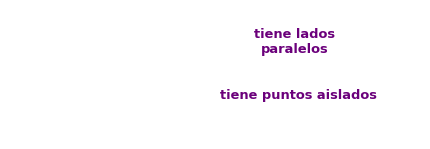
```mathematica
-Graphics--Graphics-
```

```mathematica
(* b) es un ejemplo de grafo disconexo, no se puede viajar de b a p, o de a a o, etc *)
(* a) es un ejemplo de una grafo conexo *)
```

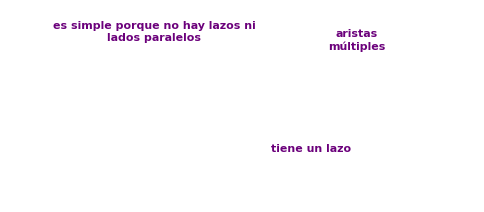
```mathematica
-Graphics--Graphics-
```

```mathematica
(*------------------------------------------------------------------------------*)
```

```mathematica
(* Comando para generar grafos de VilCretas: *)
```

```mathematica
(* Cada par representa una arista *)
```

```mathematica
(* Opciones: ?Grafo *)
```

```mathematica
(* shape -> True : pone los vertices en un circulo *)
```

```mathematica
(* Para un Grafo Dirigido, o sea con flechas, el orden importa, la flecha va de a -> h y así sucesivamentente *)
```

```mathematica
(*---------------------------------------------------------------------------*)
```

## Grafo Ponderado

```mathematica
(* Grafo Ponderado: un grafo que tiene asociadas a sus aristas un peso *)
```

```mathematica
(* Para mostrar sus pesos: *)
```

```mathematica
-Graphics--Graphics-
```

```mathematica
(* hay que poner la misma cantidad de pesos que aristas, sino no corre *)
```

```mathematica
(* Para añadir vertices aislados o puntos aislados vertices -> {w,z} *)
```

```mathematica
(*-----------------------------------------------------------------------*)
```

```mathematica
(* Para añadir aristas múltiples o lazos al grafo:  *)
```

```mathematica
(*                                      aristas múltiples, lazo  *)
```

```mathematica
(* ListasAristas[grafo] 
  ListaVertices[grafo] 
  CantAristas[grafo]
  CantNodos[grafo]  *)
```

```mathematica
(* ------------------------------------------------------------------------------- *)
```

## Definición de Ruta

```mathematica
(* Ejemplos: *)
```

```mathematica
(* Fórm: nodos - 1 = longitud *)
```

```mathematica
(*       notacion para rep ruta:        a->f->d->c->h *)
```

```mathematica
(* Si fuera un grafo ponderado: *)
```

```mathematica
(* La longitud de la ruta sería 13 *)
```

```mathematica
(*-------------------------------------------------------------------------*)
```

## Tipos de Grafos

```mathematica
(* Para ver los grafos vacíos hasta el orden que se le pase *)
```

```mathematica
(* Pued ser asi tambien:   .  .  .  .   *)
(*                         1  2  3  4   *)
```

```mathematica
GrafoVacio[13,analizar->True]
```

```mathematica
(*----------------------------------------------------------------------------------------*)
```

```mathematica
(* Es un grafo simple, no tiene lazos, el grafo completo está relacionado con todos menos con él mismo *)
(* Se denotan con una K y un num que corrsponde a su orden *)
```

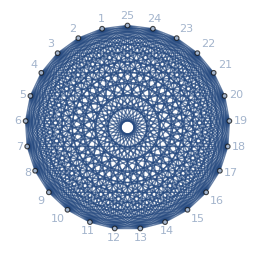

```mathematica
GrafoCompleto[25]
```

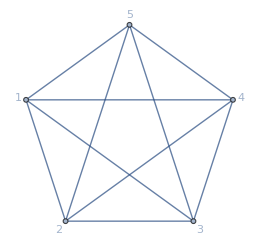

```mathematica
xd=GrafoCompleto[5]
```

```mathematica
CantAristas[xd]
```

45

```mathematica
(* Se le dan dos parametros de nodos porque el primero corresponde a la cantidad de nodos al lado izq y los otros al lado derecho: *)
(* Su notacion es K n,m *)
```

```mathematica
(* los de la derecha estám relacionados con la izquierda *)
```

```mathematica
(*-------------------------------------------------------------------------------------*)
```

## Valencia o Grado

```mathematica
(* -------------- Los lazos valen x2  *)
```

```mathematica
(* Ejemplo: *)
```

```mathematica
(* Ejemplo 5.1 *)
```

```mathematica
(* La valencia es el num de aristas incidentes al nodo *)
```

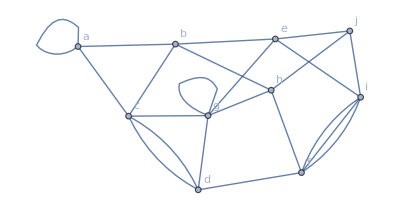

| a | b | c | e | h | d | g | f | i | j
Grado o valencia | 4 | 4 | 5 | 4 | 4 | 4 | 6 | 5 | 5 | 3

```mathematica
grafo=Grafo[{{a,a},{a,b},{a,c},{b,c},{b,e},{b,h},{c,d},{c,d},{c,g},{d,f},{d,g},{e,g},{e,i},{e,j},{f,h},{f,i},{f,i},{f,i},{g,g},{g,h},{h,j},{i,j}}]
Valencias[grafo]
```

```mathematica
(* Valencia de a es 4: tiene un lazo o sea x2 y tiene dos aristas *)
```

```mathematica
(* Devuelve un vector en vez de la tabla: *)
```

```mathematica
Valencias[grafo,table->False]
```

{4,4,5,4,4,4,6,5,5,3}

```mathematica
(*--------------------------------------------------------------------------*)
```

```mathematica
(* Valencia interna: las aristas de entran al nodo *)
(* Valencia externa: las aristas que salen del nodo *)
```

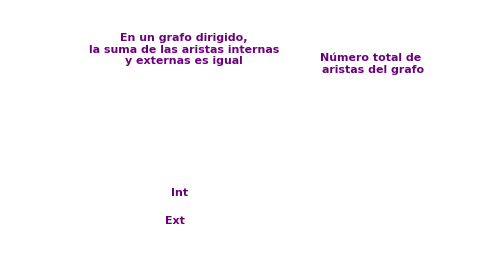
```mathematica
-Graphics--Graphics-
```

```mathematica
(* Recordar: en un grafo dirigido el orden de cada "par" importa *)
```

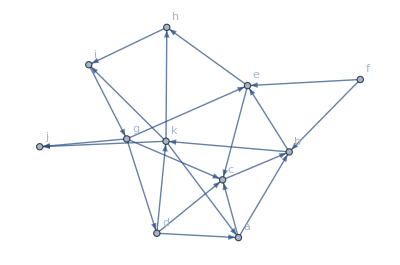

| a | b | c | k | e | d | h | f | g | j | i
Grado o valencia interna | 2 | 3 | 4 | 2 | 3 | 1 | 2 | 0 | 1 | 2 | 2
Grado o valencia externa | 2 | 2 | 1 | 4 | 2 | 3 | 1 | 2 | 4 | 0 | 1

```mathematica
grafo=Grafo[{{a,b},{a,c},{b,k},{b,e},{c,b},{d,a},{d,c},{d,k},{e,c},{e,h},{f,b},{f,e},{g,c},{g,d},{g,e},{g,j},{h,i},{i,g},{k,j},{k,a},{k,h},{k,i}},dirigido->True]
Valencias[grafo]
```

```mathematica
(* Suma valencias internas: *)
```

```mathematica
Total[Valencias[grafo][[1,1]]]
```

22

```mathematica
(* Suma valencias externas: *)
```

```mathematica
Total[Valencias[grafo][[1,2]]]
```

22

```mathematica
(*------------------------------------------------------------------------*)
```

```mathematica
GrafoCompleto[5,analizar->True]
```

```mathematica
(* Fórm para obtener la valencia de grafos completos: *)
```

```mathematica
(*--------------------------------------------------------------------------*)
```

```mathematica
GrafoBipartitoCompleto[5,6,analizar->True]
```

```mathematica
(* Fórm general para grafos bipartitos completos: *)
```

## Valencia para grafos no dirigidos

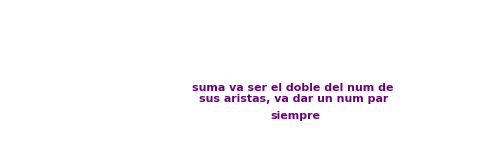
```mathematica
-Graphics--Graphics-
```

```mathematica
(* Despejando para hallar el num de aristas del grafo: *)
```

```mathematica
-Graphics--Graphics-
```

```mathematica
(* Se suman todas sus valencias y se divide entre dos *)
```

```mathematica
(*---------------------------------------------------------------------*)
```

```mathematica
(* Ejemplo 5.1 grafo: *)
```

```mathematica
grafo=Grafo[{{a,a},{a,b},{a,c},{b,c},{b,e},{b,h},{c,d},{c,d},{c,g},{d,f},{d,g},{e,g},{e,i},{e,j},{f,h},{f,i},{f,i},{f,i},{g,g},{g,h},{h,j},{i,j}}]
```

-Graphics-

```mathematica
(* Total recibe un vector y suma sus componentes *)
```

```mathematica
(* Total aca se usa para calcular el total de aristas, como este no es un grafo dirigido, la tabla de valencias solo tiene una fila, en los grafos dirigidos tiene dos filas *)
(* Se divide entre dos porque al despejar la formula asi queda *)
```

```mathematica
Total[Valencias[grafo,table->False]]/2
```

22

```mathematica
(* Al ser un grafo dirigido hay que dividir entre dos *)
```

```mathematica
(* Este comando construye un grafo a partir de la cadena de texto pasada, con un numero de aristas y nodos aleatorios *)
```

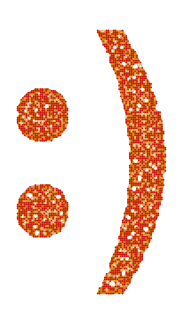

```mathematica
GrafoString[":)"]
```

```mathematica
(*-----------------------------------------------------------------------------*)
```

```mathematica
(*-------------------------------------------------------------------------------*)
```

```mathematica
(* La suma de sus valencias debe ser un num par *)
```

```mathematica
(* Como es impar no se podria construir un grafo con esas valencias *)
```

```mathematica
(* Si fuera un digrafo nos tienen que dar las valencias internas y externas *)
```

```mathematica
(*-----------------------------------------------------------------------------*)
```

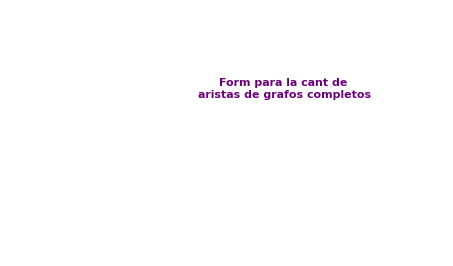
```mathematica
-Graphics--Graphics-
```

```mathematica
(* Para saber Kn teniendo la cantidad de aristas: *)
```

```mathematica
Solve[7875==(n(n-1))/2]
```

{{n→-125},{n→126}}

```mathematica
CantAristas[GrafoCompleto[126]]
```

7875

```mathematica
(*--------------------------------------------------------------------------------------*)
```

```mathematica
(*----------------------------------------------------------------------------------*)
```

```mathematica
grafo=Grafo[{{a,b},{a,c},{b,k},{b,e},{c,b},{d,a},{d,c},{d,k},{e,c},{e,h},{f,b},{f,e},{g,c},{g,d},{g,e},{g,j},{h,i},{i,g},{k,j},{k,a},{k,h},{k,i}},dirigido->True]
vector=Valencias[grafo,table->False]
```

-Graphics-

{{2,3,4,2,3,1,2,0,1,2,2},{2,2,1,4,2,3,1,2,4,0,1}}

```mathematica
{Total[vector[[1]]],Total[vector[[2]]]}
```

{22,22}

## Matriz de Adyacencia ( entre vértices )

```mathematica
(* No necesariamente la matriz de adyacencia va ser una matriz booleana, si k>1 tiene aristas múltiples y ya no será booleana *)
(* Filas y columnas son los vertices*)
```

```mathematica
(*--------------------------------------------------------------------------------*)
```

```mathematica
(* Matriz de Adyacencia: es una matriz que estudia la adyacencia entre los vértices *)
```

```mathematica
(* A mano: *)
```

```mathematica
(* Colocarse en cada vértice y ver con cuáles otros vértices se relacionan, (adyacentes) *)
(* Si se relacionan se pone 1, sino se pone 0 *)
```

```mathematica
(* Al ser un grafo simple, la matriz queda booleana *)
(* Si se varía el orden de las letras, el orden cambia, no es una matriz única *)
```

```mathematica
(* Con Mathematica: *)
```

```mathematica
(* Como no es un grafo dirigido, el orden no es importante *)
```

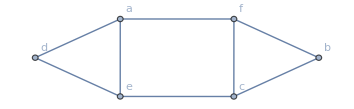

```mathematica
grafo=Grafo[{{a,e},{a,f},{a,d},{b,c},{b,f},{c,e},{c,f},{e,d}}]
```

```mathematica
(* Ahora, con ese comando, recibe el grafo, y el orden en que quiero acomodar los vertices en la matriz *)
(* El , table -> True muestra el orden de los vértices en la matriz *)
```

```mathematica
MGrafo[grafo,{a,b,c,d,e,f}]
```

(0 | 0 | 0 | 1 | 1 | 1
0 | 0 | 1 | 0 | 0 | 1
0 | 1 | 0 | 0 | 1 | 1
1 | 0 | 0 | 0 | 1 | 0
1 | 0 | 1 | 1 | 0 | 0
1 | 1 | 1 | 0 | 0 | 0)

```mathematica
MGrafo[grafo,{a,b,c,d,e,f},table->True]
```

| a | b | c | d | e | f
a | 0 | 0 | 0 | 1 | 1 | 1
b | 0 | 0 | 1 | 0 | 0 | 1
c | 0 | 1 | 0 | 0 | 1 | 1
d | 1 | 0 | 0 | 0 | 1 | 0
e | 1 | 0 | 1 | 1 | 0 | 0
f | 1 | 1 | 1 | 0 | 0 | 0

```mathematica
(* GrafoM, recibe una matriz y da el grafo *)
```

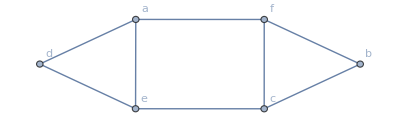

```mathematica
GrafoM[({{0, 0, 0, 1, 1, 1}, {0, 0, 1, 0, 0, 1}, {0, 1, 0, 0, 1, 1}, {1, 0, 0, 0, 1, 0}, {1, 0, 1, 1, 0, 0}, {1, 1, 1, 0, 0, 0}}),{a,b,c,d,e,f}]
```

```mathematica
(* Con matriz -> True devuleve lo que es para mathematica es una matriz, el arreglo rectangular *)
```

```mathematica
MGrafo[grafo,{a,b,c,d,e,f},matriz->True]
```

{{0,0,0,1,1,1},{0,0,1,0,0,1},{0,1,0,0,1,1},{1,0,0,0,1,0},{1,0,1,1,0,0},{1,1,1,0,0,0}}

```mathematica
(*------------------------------------------------------------------*)
```

```mathematica
(* Este grafo tiene lados paralelos o aristas múltiples: un vértice se relaciona con otro más de una vez *)
```

```mathematica
(* En el caso de los vétices que se relacionan más de una vez con otros, se coloca en la matriz la cantidad de veces que se relacionan *)
```

```mathematica
(* Con Mathematica: *)
```

```mathematica
grafo=Grafo[{{a,a},{a,a},{a,b},{a,b},{a,g},{b,b},{b,d},{b,e},{b,f},{c,a},{c,d},{c,d},{c,d},{c,d},{d,e},{e,f},{e,f},{e,f},{f,g}}];
```

```mathematica
(* ListaVertices hace que se pueda ordenar los vértices alfabéticamente, solo se puede usar si la matriz de esta construyendo con el orden del abecedario *)
(* Hay que tener cuidado con GrafoM con ListaVertices, hay que tener presente el orden de los vertices que fue usado en la matriz *)
```

```mathematica
MGrafo[grafo,ListaVertices[grafo]]
```

(2 | 2 | 1 | 0 | 0 | 0 | 1
2 | 1 | 0 | 1 | 1 | 1 | 0
1 | 0 | 0 | 4 | 0 | 0 | 0
0 | 1 | 4 | 0 | 1 | 0 | 0
0 | 1 | 0 | 1 | 0 | 3 | 0
0 | 1 | 0 | 0 | 3 | 0 | 1
1 | 0 | 0 | 0 | 0 | 1 | 0)

```mathematica
MGrafo[grafo,ListaVertices[grafo],table->True]
```

| a | b | c | d | e | f | g
a | 2 | 2 | 1 | 0 | 0 | 0 | 1
b | 2 | 1 | 0 | 1 | 1 | 1 | 0
c | 1 | 0 | 0 | 4 | 0 | 0 | 0
d | 0 | 1 | 4 | 0 | 1 | 0 | 0
e | 0 | 1 | 0 | 1 | 0 | 3 | 0
f | 0 | 1 | 0 | 0 | 3 | 0 | 1
g | 1 | 0 | 0 | 0 | 0 | 1 | 0

```mathematica
(* Para reconstruir enl grafo: *)
```

```mathematica
MGrafo[MGrafo[grafo,ListaVertices[grafo],matriz->True],ListaVertices[grafo]]
```

## Propiedades de la matriz de adyacencia de un grafo No Dirigido

```mathematica
(*------------------------------------------------------------------------------*)
```

```mathematica
(* Matriz de adyacencia con un grafo dirigido *)
```

```mathematica
(* Hay que fijasrse en las flechas de cada vértice *)
```

```mathematica
(* Suma de filas da valencia externa, y suma de columnas da valencia interna *)
```

```mathematica
(* Con Mathematica: *)
```

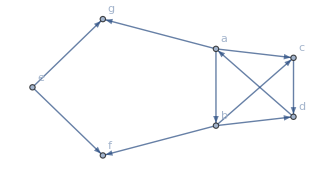

(0 | 1 | 1 | 0 | 0 | 0 | 1
0 | 0 | 1 | 1 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
grafo=Grafo[{{a,b},{a,c},{a,g},{b,c},{b,d},{b,f},{c,d},{d,a},{e,f},{e,g}},dirigido->True]
MGrafo[grafo,{a,b,c,d,e,f,g}]
```

```mathematica
MGrafo[grafo,{a,b,c,d,e,f,g},table->True]
```

| a | b | c | d | e | f | g
a | 0 | 1 | 1 | 0 | 0 | 0 | 1
b | 0 | 0 | 1 | 1 | 0 | 1 | 0
c | 0 | 0 | 0 | 1 | 0 | 0 | 0
d | 1 | 0 | 0 | 0 | 0 | 0 | 0
e | 0 | 0 | 0 | 0 | 0 | 1 | 1
f | 0 | 0 | 0 | 0 | 0 | 0 | 0
g | 0 | 0 | 0 | 0 | 0 | 0 | 0

## Propiedad de la matriz de adyacencia de un Grafo Simple

```mathematica
(* El teorema asume que en ruta se pueden repetir aristas, lo que por definición de ruta, no funciona así, entonces, la matriz que se calcula a la hora de aplicar el teorema es la cantidad máxima de rutas de longitud k *)
```

```mathematica
(*--------------------------------------------------------------------*)
```

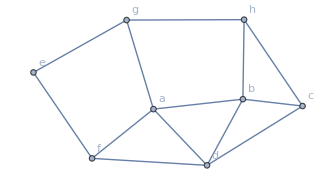

```mathematica
grafo=Grafo[{{a,b},{a,f},{a,g},{b,c},{b,d},{b,h},{c,d},{c,h},{d,a},{d,f},{e,f},{e,g},{g,h}}]
```

```mathematica
(* CantMRutas automatiza la construcción de una matriz de adyacencia, así como la cantidad de rutas hasta k *)
CantMRutas[grafo,4]
```

```mathematica
MGrafo[grafo,]
```

```mathematica
(* Esta matriz es el resultado de haber tomado la matriz de adyacencia del grafo y haberla elevado a la 4 *)
```

| a | b | c | d | e | f | g | h
a | 34 | 20 | 21 | 27 | 16 | 13 | 8 | 23
b | 20 | 34 | 23 | 26 | 5 | 23 | 22 | 15
c | 21 | 23 | 21 | 19 | 6 | 15 | 13 | 14
d | 27 | 26 | 19 | 32 | 12 | 16 | 14 | 22
e | 16 | 5 | 6 | 12 | 10 | 3 | 1 | 11
f | 13 | 23 | 15 | 16 | 3 | 20 | 18 | 7
g | 8 | 22 | 13 | 14 | 1 | 18 | 19 | 5
h | 23 | 15 | 14 | 22 | 11 | 7 | 5 | 20

```mathematica
(* Ese 6 corresponde al número máximo de rutas distintas que se pueden formar del nodo c al nodo e PERMITIENDO que se repitan las aristas *)
(* En este caso, 6, si es el numero exacto de rutas, pero no siempre pasa esto *)
```

```mathematica
CantMRutas[grafo,10,all->True]
```

Part::partd: Part specification Null⟦1⟧ is longer than depth of object.

VertexList::graph: A graph object is expected at position 1 in VertexList[VilCretas`Private`GGrafoAuxiliar17].

TableForm::tfh: TableHeadings option contained VertexList[VilCretas`Private`GGrafoAuxiliar17], which is not Automatic, None, or a list of labels.

Part::partd: Part specification Null⟦1⟧ is longer than depth of object.

VertexList::graph: A graph object is expected at position 1 in VertexList[VilCretas`Private`GGrafoAuxiliar17].

TableForm::tfh: TableHeadings option contained VertexList[VilCretas`Private`GGrafoAuxiliar17], which is not Automatic, None, or a list of labels.

Part::partd: Part specification Null⟦1⟧ is longer than depth of object.

VertexList::graph: A graph object is expected at position 1 in VertexList[VilCretas`Private`GGrafoAuxiliar17].

TableForm::tfh: TableHeadings option contained VertexList[VilCretas`Private`GGrafoAuxiliar17], which is not Automatic, None, or a list of labels.

Part::partd: Part specification Null⟦1⟧ is longer than depth of object.

VertexList::graph: A graph object is expected at position 1 in VertexList[VilCretas`Private`GGrafoAuxiliar17].

TableForm::tfh: TableHeadings option contained VertexList[VilCretas`Private`GGrafoAuxiliar17], which is not Automatic, None, or a list of labels.

## Propiedad de la matriz de adyacencia de un Grafo Simple Ponderado

```mathematica
(* Ejemplo de una Matriz de adyacencia de pesos: *)
```

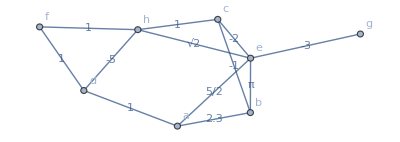

```mathematica
A=({{0, 2.3, 0, 1, 5/2, 0, 0, 0}, {2.3, 0, -1, 0, π, 0, 0, 0}, {0, -1, 0, 0, -2, 0, 0, 1}, {1, 0, 0, 0, 0, 1, 0, -5}, {5/2, π, -2, 0, 0, 0, -3, √2}, {0, 0, 0, 1, 0, 0, 0, 1}, {0, 0, 0, 0, -3, 0, 0, 0}, {0, 0, 1, -5, √2, 1, 0, 0}});
(* Se utiliza GrafoMP *)
GrafoMP[A,{a,b,c,d,e,f,g,h},mostrarpesos->True]
```

## Matriz de Incidencia ( entre aristas )

```mathematica
(* Estudia la incidencia entre las aristas *)
(* Siempre va ser booleana *)
(* Las filas, van a ser los nodos y las columnas son las aristas del grafo *)
(* Esta no necesariamente va ser una matriz cuadrada a diferencia de la matriz de adyacencia que siempre es cuadrada *)
(* Comparte la propiedad de la suma de las filas: que da la valencia del nodo siempre y cuando no haya un lazo *)
```

```mathematica
(*---------------------------------------------------------------------------*)
```

```mathematica
(* Ejemplo 5.11: *)
```

```mathematica
(* Igualmente, no es única *)
```

```mathematica
(* Esta es mejor construirla por columnas *)
(* Nos colocamos sobre una arista, y nos fijamos donde en que vertices incide, o sea, cuales son los vertices de esa arista *)
```

```mathematica
(* A mano: *)
```

```mathematica
(* Se etiquetan las aristas en el grafo en el orden que uno quiera *)
```

```mathematica
(* Con Mathematica: *)
```

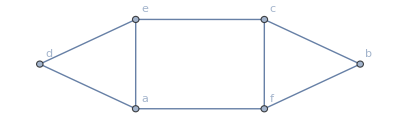

(1 | 1 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 1 | 1 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 0 | 1 | 0 | 1
0 | 0 | 1 | 0 | 1 | 0 | 1 | 0)

```mathematica
grafo=Grafo[{{a,d},{a,e},{a,f},{b,c},{b,f},{c,e},{c,f},{d,e}}]
(* Se utiliza MIGrafo, I de incidencia, sin table solo da la matriz *)
MIGrafo[grafo,ListaVertices[grafo]]
```

```mathematica
(* con table->True se pueden ver las aristas mas claramente *)
```

```mathematica
MIGrafo[grafo,ListaVertices[grafo],table->True]
```

| a<->d | a<->e | a<->f | b<->c | b<->f | c<->e | c<->f | d<->e
a | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0
b | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0
c | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0
d | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1
e | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 1
f | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 0

```mathematica
(* Ahora, si quiero cambiar el orden de las aristad se utiliza edgesgraph  *)
```

```mathematica
MIGrafo[grafo,ListaVertices[grafo],table->True,edgesgraph->{{a,f},{a,d},{a,e},{b,c},{c,e},{c,f},{d,e},{b,f}}]
```

| a<->f | a<->d | a<->e | b<->c | c<->e | c<->f | d<->e | b<->f
a | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0
b | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1
c | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0
d | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0
e | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 0
f | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 1

```mathematica
(* Si se tuvieran aristas multiples, esto lo que causa es que se tenga que agregar mas columnas a la matriz *)
(* Ejemplo: *)
```

```mathematica
(* Para construir el grafo, a partir de una matriz: *)
```

```mathematica
GrafoMI[({{1, 1, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 1, 0, 0, 0}, {0, 0, 0, 1, 0, 1, 1, 0}, {1, 0, 0, 0, 0, 0, 0, 1}, {0, 1, 0, 0, 0, 1, 0, 1}, {0, 0, 1, 0, 1, 0, 1, 0}}),ListaVertices[grafo]]
```

-Graphics-

```mathematica
(*-----------------------------------------------------------------------------*)
```

```mathematica
(* Matriz de incidencia de un digrafo *)
```

```mathematica
(* Hay que especificar el vertice de partida, las aristas tienen direccion *)
```

```mathematica
(* Se va a utilizar un -1 para el vertice de partida y un 1 para el vertice de llegada *)
```

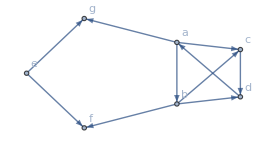

```mathematica
grafo=Grafo[{{a,b},{a,c},{a,g},{b,c},{b,d},{b,f},{c,d},{d,a},{e,f},{e,g}},dirigido->True]
```

```mathematica
MIGrafo[grafo,{a,b,c,d,e,f,g},table->True]
```

| a->b | a->c | a->g | b->c | b->d | b->f | c->d | d->a | e->f | e->g
a | -1 | -1 | -1 | 0 | 0 | 0 | 0 | 1 | 0 | 0
b | 1 | 0 | 0 | -1 | -1 | -1 | 0 | 0 | 0 | 0
c | 0 | 1 | 0 | 1 | 0 | 0 | -1 | 0 | 0 | 0
d | 0 | 0 | 0 | 0 | 1 | 0 | 1 | -1 | 0 | 0
e | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1
f | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0
g | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1

## Circuitos en un Grafo

```mathematica
(* Un circuito es cualquier ruta de un grafo que inicie y finalice en el mismo vértice *)
```

```mathematica
(* Son tipos de trayectorias o rutas, son sucesiones de aristas que van a unir un vertice con el mismo *)
(* Todo lazo es un circuito de longuitud 1 *)
(* Cuando hay un circuitos que no repite vertices, se le denomia circuito simple *)
(* Cuando hay un cicuito que contiene todas las aristas de un grafo (pasando una única vez por ellas), se le llama circuito de Euler *)
(* Cuando hay un cicuito que contiene todas los vertices de un grafo (pasando una única vez por ellos), se le llama circuito de Hamilton *)
```

```mathematica
(* Si el vertice de partida y de llegada coinciden, habiendo pasado por todas las aristas del grafo una unica vez, es un circuito de euler *)
(* Si paso una única vez por todas las aristas del grafo y los vertices de llegada y partida no coiciden es una ruta de Euler *)
```

```mathematica
(* Lo mismo pasa con los cicuitos y rutas de Hamilton *)
```

```mathematica
(*--------------------------------------------------------------------------------------------*)
```

```mathematica
(* Representación de circuitos: *)
```

```mathematica
(* Las valencias de c y h en el grafo c es 3, son los únicos que tienen valencias impares. Se verá un teorema que usa esto *)
```

```mathematica
(*------------------------------------------------------------------------------------*)
```

```mathematica
(* Euler descubrió que para poder pasar una única vez por todas los puentes o aristas, la valencia de los nodos debe de ser par, porque se necesita una arista para entrar y otra distinta para salir *)
```

```mathematica
(* En este caso es imposible hacer ese recorrido *)
```

```mathematica
(* Para tener un circuito de euler se necesita que las valencias de los nodos sean pares *)
```

```mathematica
(*----------------------------------------------------------------------------*)
```

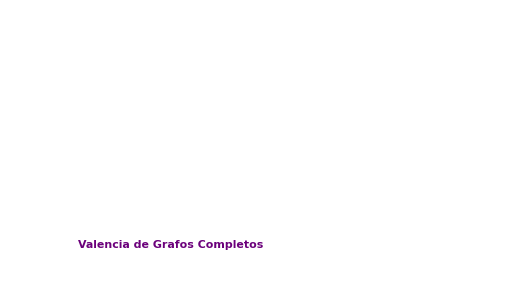
```mathematica
-Graphics--Graphics-
```

```mathematica
(*------------------------------------------------------------------------------------*)
```

```mathematica
-Graphics--Graphics-
```

## Algoritmo de Fleury

```mathematica
(*--------------------------------------------------------------------------*)
```

```mathematica
(* Utilizando el algoritmo de Fleury, antes aseegurarse que todas las valencias de los nodos son pares *)
```

```mathematica
(* Manualmente: *)
```

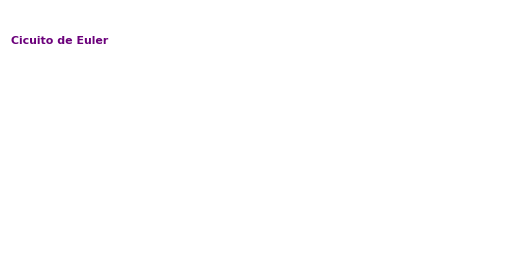
```mathematica
-Graphics--Graphics-
```

```mathematica
(* Luego de la iteracion #2, los nodos h,b,a quedan aislados, por lo que tambien se eliminan, segun el algoritmo *)
(* Por lo que en la iteracion #3, se debe comenzar en e *)
```

```mathematica
grafo=Grafo[{{a,d},{a,e},{a,g},{a,h},{b,e},{b,f},{c,d},{c,e},{d,e},{d,g},{e,f},{g,h},{g,e},{b,c},{f,h},{h,b},{f,c}}];
```

```mathematica
(* Indica si el grafo contiene algun circuito de euler *)
```

```mathematica
CircuitoEulerQ[grafo]
```

True

```mathematica
(* Se le pasa un grafo y la cantidad de circuitos de euler que se quiere encontrar *)
```

```mathematica
(* ruta -> True permite animar alguna de las rutas y ver la trayectoria *)
```

```mathematica
CircuitosEuler[grafo,4,ruta->True]
```

{{a<->d,d<->g,g<->e,e<->f,f<->c,c<->b,b<->h,h<->f,f<->b,b<->e,e<->d,d<->c,c<->e,e<->a,a<->h,h<->g,g<->a},{a<->d,d<->g,g<->e,e<->f,f<->c,c<->b,b<->h,h<->f,f<->b,b<->e,e<->d,d<->c,c<->e,e<->a,a<->g,g<->h,h<->a},{a<->d,d<->g,g<->e,e<->f,f<->c,c<->b,b<->h,h<->f,f<->b,b<->e,e<->c,c<->d,d<->e,e<->a,a<->h,h<->g,g<->a},{a<->d,d<->g,g<->e,e<->f,f<->c,c<->b,b<->h,h<->f,f<->b,b<->e,e<->c,c<->d,d<->e,e<->a,a<->g,g<->h,h<->a}}

Ruta de la animación: {a<->d,d<->g,g<->e,e<->f,f<->c,c<->b,b<->h,h<->f,f<->b,b<->e,e<->c,c<->d,d<->e,e<->a,a<->h,h<->g,g<->a}

OptionValue::optnf: 
   Option name VilCretas`padding not found in defaults for 
    VilCretas`AnimarGrafo.

Iteración: 1

Aristas añadidas: {{a,d}}

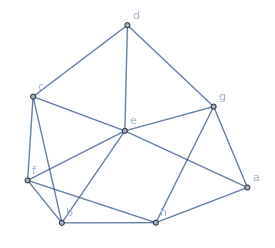

Iteración: 2

Aristas añadidas: {{a,d},{d,c}}

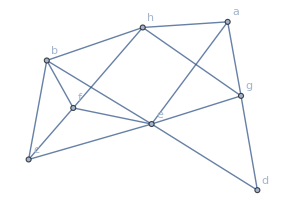

Iteración: 3

Aristas añadidas: {{a,d},{d,c},{c,b}}

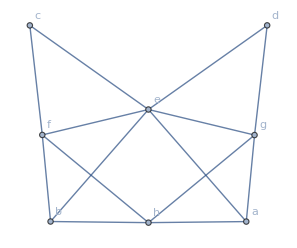

Iteración: 4

Aristas añadidas: {{a,d},{d,c},{c,b},{b,e}}

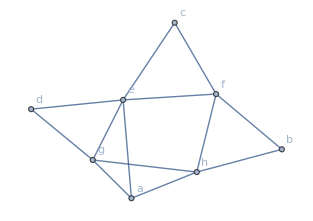

Iteración: 5

Aristas añadidas: {{a,d},{d,c},{c,b},{b,e},{e,a}}

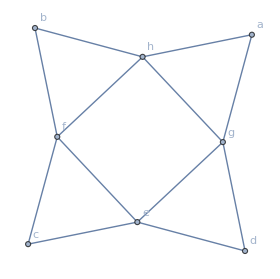

Iteración: 6

Aristas añadidas: {{a,d},{d,c},{c,b},{b,e},{e,a},{a,g}}

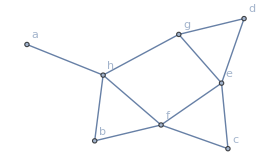

Iteración: 7

Aristas añadidas: {{a,d},{d,c},{c,b},{b,e},{e,a},{a,g},{g,d}}

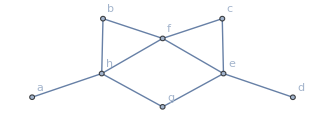

Iteración: 8

Aristas añadidas: {{a,d},{d,c},{c,b},{b,e},{e,a},{a,g},{g,d},{d,e}}

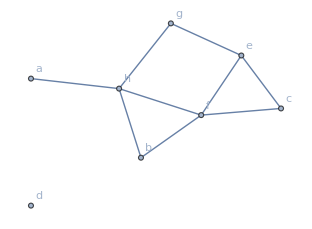

Iteración: 9

Aristas añadidas: {{a,d},{d,c},{c,b},{b,e},{e,a},{a,g},{g,d},{d,e},{e,c}}

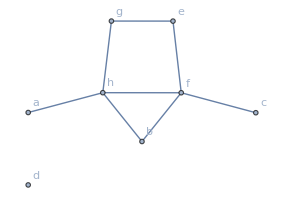

Iteración: 10

Aristas añadidas: {{a,d},{d,c},{c,b},{b,e},{e,a},{a,g},{g,d},{d,e},{e,c},{c,f}}

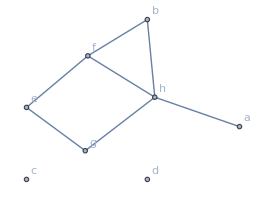

Iteración: 11

Aristas añadidas: {{a,d},{d,c},{c,b},{b,e},{e,a},{a,g},{g,d},{d,e},{e,c},{c,f},{f,b}}

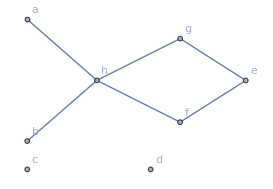

Iteración: 12

Aristas añadidas: {{a,d},{d,c},{c,b},{b,e},{e,a},{a,g},{g,d},{d,e},{e,c},{c,f},{f,b},{b,h}}

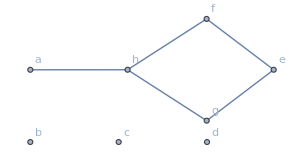

Iteración: 13

Aristas añadidas: {{a,d},{d,c},{c,b},{b,e},{e,a},{a,g},{g,d},{d,e},{e,c},{c,f},{f,b},{b,h},{h,f}}

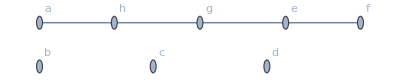

Iteración: 14

Aristas añadidas: {{a,d},{d,c},{c,b},{b,e},{e,a},{a,g},{g,d},{d,e},{e,c},{c,f},{f,b},{b,h},{h,f},{f,e}}

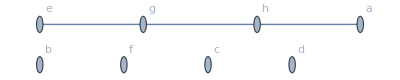

Iteración: 15

Aristas añadidas: {{a,d},{d,c},{c,b},{b,e},{e,a},{a,g},{g,d},{d,e},{e,c},{c,f},{f,b},{b,h},{h,f},{f,e},{e,g}}

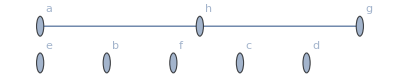

Iteración: 16

Aristas añadidas: {{a,d},{d,c},{c,b},{b,e},{e,a},{a,g},{g,d},{d,e},{e,c},{c,f},{f,b},{b,h},{h,f},{f,e},{e,g},{g,h}}

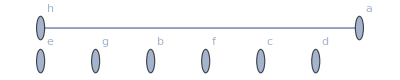

Iteración: 17

Aristas añadidas: {{a,d},{d,c},{c,b},{b,e},{e,a},{a,g},{g,d},{d,e},{e,c},{c,f},{f,b},{b,h},{h,f},{f,e},{e,g},{g,h},{h,a}}

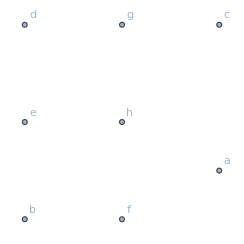

Un circuito de Euler mediante una representación de nodos es: {a,d,c,b,e,a,g,d,e,c,f,b,h,f,e,g,h,a}

El mismo circuito representado a través de aristas es: {{a,d},{d,c},{c,b},{b,e},{e,a},{a,g},{g,d},{d,e},{e,c},{c,f},{f,b},{b,h},{h,f},{f,e},{e,g},{g,h},{h,a}}

```mathematica
Fleury[grafo]
```

```mathematica
(*----------------------------------------------------------------------------------*)
```

```mathematica
Valencias[grafo]
```

| a | e | d | f | h | c | g | b
Grado o valencia | 4 | 6 | 6 | 4 | 2 | 4 | 4 | 4

```mathematica
(* Todas son pares, por lo que se puede aplicar el algoritmo *)
```

```mathematica
(* Manualmente: *)
```

```mathematica
(* La d aparece dos veces, solo se puede cambiar una vez *)
```

```mathematica
grafo=Grafo[{{a,e},{d,f},{e,f},{a,d},{d,e},{h,c},{h,g},{a,f},{b,d},{b,e},{b,g},{c,d},{c,e},{c,f},{d,g},{e,g},{a,b}}];
```

## Teorema para calcular Rutas de Euler

```mathematica
(* Es imposible que un circuito tenga un circuito y una ruta de euler *)
```

```mathematica
(*------------------------------------------------------------------------------------*)
```

```mathematica
(* Con el algoritmo de Fleury: *)
```

```mathematica
(* Eliminar temporalmente la arista que une a con b y aplicar el algoritmo de Fleury, ya esos nodos tendrian valencia par *)
```

```mathematica
(* Obligatoriamente se tiene que empezar con a o con b *)
```

```mathematica
(* Al final se agrega al final o al inicio alguno de los nodos de la arista que fue eliminada, al principio seria b->a y al final seria a-> b *)
```

```mathematica
grafo=Grafo[{{a,b},{a,d},{a,e},{a,f},{a,g},{b,c},{b,d},{b,f},{b,g},{c,d},{c,e},{c,f},{d,e},{d,f},{d,g},{e,f},{f,g}}];
```

```mathematica
Valencias[grafo]
```

| a | b | d | e | f | g | c
Grado o valencia | 5 | 5 | 6 | 4 | 6 | 4 | 4

```mathematica
(* Tiene o no una ruta de euler *)
```

```mathematica
RutaEulerQ[grafo]
```

True

```mathematica
RutaEuler[grafo]
```

{{a,d},{d,b},{b,c},{c,d},{d,e},{e,a},{a,f},{f,b},{b,g},{g,d},{d,f},{f,c},{c,e},{e,f},{f,g},{g,a},{a,b}}

```mathematica
(*----------------------------------------------------------------------------------------------*)
```

```mathematica
(* Caso en que los nodos que tienen valencia impar no esten unidos por una arista *)
```

```mathematica
(* Siempre hay que revisar las valencias de los nodos antes *)
```

```mathematica
(* En el ejemplo anterior, la arista se elimina, en este se agrega para unir los nodos de valencia impar *)
```

```mathematica
(* Ahora todos los nodos quedarian con valencia par: *)
```

```mathematica
(* Importante: al usar el algoritmo hay que empezar con la arista que se acaba de agregar *)
```

```mathematica
(* Al final se quita el nodo inicial de la arista agregada *)
```

```mathematica
grafo=Grafo[{{c,e},{d,e},{d,a},{c,d},{e,h},{c,h},{c,f},{a,b},{a,c},{b,c},{b,d},{b,h},{d,f},{e,f},{f,g},{a,g},{g,d}}];
```

```mathematica
RutaEulerQ[grafo]
```

True

```mathematica
RutaEuler[grafo]
```

{{h,b},{b,a},{a,c},{c,b},{b,d},{d,c},{c,e},{e,d},{d,a},{a,g},{g,f},{f,c},{c,h},{h,e},{e,f},{f,d},{d,g}}

```mathematica
RutaEuler[grafo,ruta->True]
```

OptionValue::optnf: 
   Option name VilCretas`padding not found in defaults for 
    VilCretas`AnimarGrafo.

## Propiedades para Circuitos de Hamilton

```mathematica
(* Recordar: un grafo simple es un grafo que no tiene aristas múltiples ni lazos *)
(* Un grafo conexo quiere decir que cada par de nodos existen una ruta que los une *)
```

```mathematica
(* Si alguna de estas propiedades es verdadera se puede garantizar la existencia de un cicuito de hamilton, pero aunque alguna sea falsa, no se puede afirmar que ya no existe un circuito de hamilton *)
```

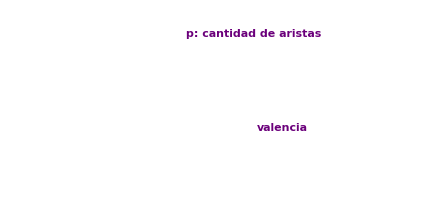
```mathematica
-Graphics--Graphics-
```

```mathematica
(* Teoremas en ejemplos: *)
```

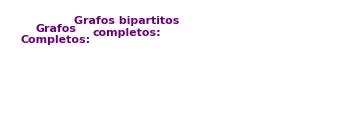
```mathematica
-Graphics--Graphics-
```

```mathematica
(* Para grafos completos: *)
```

```mathematica
(* Para que un grafo completo, tenga un cicuito de hamilton el orden debe de ser mayor o igual a 3 *)
Reduce[n(n-1)/2>=(n^2-3n+6)/2,n]
```

n≥3

```mathematica
(* Cualquier grafo que tenga un circuito va a tener un circuito de hamilton *)
```

```mathematica
(* Para grafos bi partitos completos: *)
```

```mathematica
Reduce[m>=(n+m)/2&&n>=(n+m)/2]
```

n∈ℝ&&m==n

```mathematica
(* Un grafo bi partito completo va a tener un cicuito de hamilton siempre y cuando m y n sean iguales a partir del orden 2 *)
```

```mathematica
(*----------------------------------------------------------------------------------*)
```

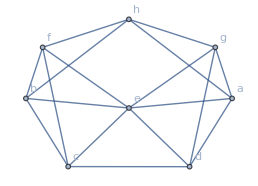

```mathematica
grafo=Grafo[{{a,d},{a,e},{a,g},{a,h},{b,e},{b,f},{c,d},{c,e},{d,e},{d,g},{e,f},{g,h},{g,e},{b,c},{f,h},{h,b},{f,c}}]
```

```mathematica
(* Calcular las valencias del grafo: *)
```

```mathematica
Valencias[grafo]
```

| a | d | e | g | h | b | f | c
Grado o valencia | 4 | 4 | 6 | 4 | 4 | 4 | 4 | 4

```mathematica
(* Propiedad #1: *)
```

```mathematica
(* Calcular el numero de aristas: *)
```

```mathematica
Total[Valencias[grafo,table->False]]/2
```

17

```mathematica
(* O con el comando: *)
```

```mathematica
p=CantAristas[grafo]
```

17

```mathematica
(* Para saber la cantidad de nodos: *)
n=CantNodos[grafo]
```

8

```mathematica
(* Ahora, ver si cumple la propiedad #1 *)
```

```mathematica
p>=(n^2-3n+6)/2
```

False

```mathematica
(* No cumple, por lo que se sigue a comprobar la siguiente propiedad: *)
```

```mathematica
(* Propiedad #2: todas las valencias deben de ser mayor o iguales a n/2 *)
```

```mathematica
Valencias[grafo]
```

| a | d | e | g | h | b | f | c
Grado o valencia | 4 | 4 | 6 | 4 | 4 | 4 | 4 | 4

```mathematica
(* Si sumple con esta propiedad, por lo tanto se comprueba que se puede encontrar un circuito de hamilton *)
```

```mathematica
(* Ya se comprueba que si tiene circuito de hamilton, pero para ver como se calcula la propiedad #3 :*)
```

```mathematica
(* Propiedad #3: buscar los vertices no adyacentes y ver si cumplen con que la valencia del priemero +  la del segundo es mayor o igual a n *)
```

```mathematica
(* El complemento de un grafo lo que hace es a los nodos que estan relacionados, dejarlos sin relacionar y viceversa *)
```

```mathematica
(* Con estos comandos podemos ver la lista de nodos que originalmente no son adyacentes *)
```

```mathematica
ListaAristas[GraphComplement[grafo]]
```

{{a,b},{a,c},{a,f},{d,b},{d,f},{d,h},{e,h},{g,b},{g,c},{g,f},{h,c}}

```mathematica
(* Ahora comprobar que si se cumpla que la suma de las valencias de cada par sea >= a n que en este caso es 8 *)
```

```mathematica
(* Se cumple la propiedad, todas las sumas son >= a n *)
```

```mathematica
(* Devuelve verdadero o falso, si el grafo contiene un circuito de hamilton *)
```

```mathematica
CircuitoHamiltonQ[grafo]
```

True

```mathematica
(* Muestra la cantidad de cicuitos de hamilton que se le pase *)
```

```mathematica
CircuitosHamilton[grafo,4]
```

{{a<->d,d<->c,c<->e,e<->f,f<->b,b<->h,h<->g,g<->a},{a<->g,g<->d,d<->c,c<->e,e<->f,f<->b,b<->h,h<->a},{a<->d,d<->c,c<->e,e<->b,b<->f,f<->h,h<->g,g<->a},{a<->g,g<->d,d<->c,c<->e,e<->b,b<->f,f<->h,h<->a}}

```mathematica
ExisteCircuitoHamilton[grafo]
```

Se satisface la propiedad de Ore

Se cumple la propiedad de Dirac

No se satisface la propiedad de la cantidad de aristas, m = 17 < n^2/2 = 23

Existe un circuito de Hamilton

```mathematica
(*--------------------------------------------------------------------------------*)
```

```mathematica
(* Grafo del 5.26: *)
```

```mathematica
grafo=Grafo[{{a,e},{d,f},{e,f},{a,d},{d,e},{h,c},{h,g},{a,f},{b,d},{b,e},{b,g},{c,d},{c,e},{c,f},{d,g},{e,g},{a,b}}];
```

```mathematica
(* Primer Propiedad: *)
```

```mathematica
p=CantAristas[grafo]
```

17

```mathematica
n=CantNodos[grafo]
```

8

```mathematica
p>=(n^2-3 n+6)/2
```

False

```mathematica
(* Primer propiedad falsa, la cantidad de aristas no es >= a la formula *)
```

```mathematica
(* Segunda Propiedad: *)
```

```mathematica
Valencias[grafo]
```

| a | e | d | f | h | c | g | b
Grado o valencia | 4 | 6 | 6 | 4 | 2 | 4 | 4 | 4

```mathematica
(* No todas las valencias son mayores a n/2, no se cumple la segunda propiedad *)
```

```mathematica
(* Tercera Propiedad: *)
```

```mathematica
ListaAristas[GraphComplement[grafo]]
```

{{a,c},{a,g},{a,h},{c,b},{c,g},{d,h},{e,h},{f,b},{f,g},{f,h},{h,b}}

```mathematica
(* La suma de las valencias de f y g = 6 no es >= a n/2 *)
```

```mathematica
(* Y aun asi, el grafo tiene un cicuito de hamilton: *)
```

```mathematica
HamiltonianGraphQ[grafo]
```

True

```mathematica
(* Se halla el circuito de hamilton a mano: *)
```

```mathematica
(*---------------------------------------------------------------------------------*)
```

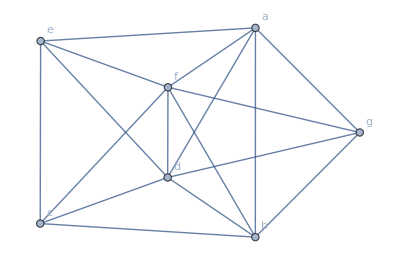

```mathematica
grafo=Grafo[{{a,b},{a,d},{a,e},{a,f},{a,g},{b,c},{b,d},{b,f},{b,g},{c,d},{c,e},{c,f},{d,e},{d,f},{d,g},{e,f},{f,g}}]
```

```mathematica
(* Primer Propiedad*)
```

```mathematica
p=CantAristas[grafo]
```

17

```mathematica
n=CantNodos[grafo]
```

7

```mathematica
p>=(n^2-3 n+6)/2
```

True

```mathematica
(* Sí es verdadera, por lo que tiene un cicuito de hamilton *)
```

```mathematica
(* Igual la segunda propiedad se cumple, todas las valencias de los nodos son mayores o iguales a n/2 *)
```

```mathematica
Valencias[grafo]
```

| a | b | d | e | f | g | c
Grado o valencia | 5 | 5 | 6 | 4 | 6 | 4 | 4

```mathematica
(*----------------------------------------------------------------------------------------*)
```

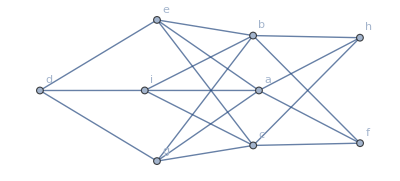

```mathematica
grafo=Grafo[{{a,e},{a,f},{a,g},{a,h},{a,i},{b,e},{b,f},{b,g},{b,h},{b,i},{c,e},{c,f},{c,g},{c,h},{c,i},{d,e},{d,g},{d,i}}]
```

```mathematica
ExisteCircuitoHamilton[grafo]
```

No se satisface la propiedad de Ore, un contraejemplo ocurre en: Valencia[a] + Valencia[d] = 8 < n = 9

No se cumple la propiedad de Dirac, un contrajemplo ocurre en: Valencia[e] = 4 < n/2 = 9/2

No se satisface la propiedad de la cantidad de aristas, m = 18 < n^2/2 = 30

No hay criterio, sin embargo, el valor lógico sobre la existencia de un circuito de Hamilton en el grafo es: False

## Algoritmo del camino más corto (Algoritmo de Dijkstra)

```mathematica
(*---------------------------------------------------------------------------------*)
```

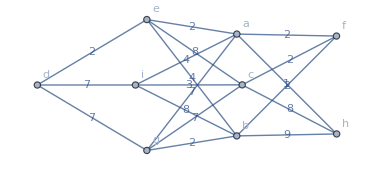

```mathematica
A=({{0, 0, 0, 0, 2, 2, 7, 1, 4}, {0, 0, 0, 0, 4, 2, 2, 9, 8}, {0, 0, 0, 0, 8, 2, 7, 8, 3}, {0, 0, 0, 0, 2, 0, 7, 0, 7}, {2, 4, 8, 2, 0, 0, 0, 0, 0}, {2, 2, 2, 0, 0, 0, 0, 0, 0}, {7, 2, 7, 7, 0, 0, 0, 0, 0}, {1, 9, 8, 0, 0, 0, 0, 0, 0}, {4, 8, 3, 7, 0, 0, 0, 0, 0}});
grafo=GrafoMP[A,{a,b,c,d,e,f,g,h,i},mostrarpesos->True]
```

```mathematica
(* 1. Nodo d es el nodo de partida, así que la primera vez se le pone 0 y a los otros infinito *)
(* 2. Se eliminina d y se busca cuál es la marca más pequeña, en este caso es e , se suma lo que tiene d con e o sea 0+2 = 2 *)
```

```mathematica
(* 3. Se hace lo mismo con g e i *)
```

```mathematica
(* 4. En la iteración se hace lo mismo, se vuelve a seleccionar la marca más pequeña, en este caso es 2 *)
```

```mathematica
(* 5. Se suma el 2 de la arista de a + el 2 de la arista de e = 4 y se ponen e, que es de dónde proviene, lo mismo con c y b *)
```

```mathematica
(* 6. En la 3 iteración se hace lo mismo, se escoje al nodo con la arista que tenga el peso más pequeño, en este caso es a con 4*)
(*7. Se elimina a y se marcan las aristas con las que está relacionada a, y se actualizan los pesos o las marcas de esas aristas *)
```

```mathematica
(* 8. En el caso de i, el peso de la arista que va de a a i tiene peso 4, y se le suma el peso de a que es 4, y da como resultado 8, pero se escoje el más pequeño entre ese y la marca de i, o sea 7, entonces el valor no se cambia y queda 7 *)
(* 8. Pasa lo mismo con g, la suma es 11 y la marca es 7 *)
(* 9. En h, el peso de la arista que une a a con h es 1, entonces 1+4=5 y el más pequeño entre infinito y 5 es 5, por lo que se pone que la marca de h es {5,a} la es de dónde proviene *)
(* 10. En f queda 6,a porque 4+2=6 y la marca que traía es infinita *)
(* 11. En la 4 iteración, se escoje a h porque el peso de arista es el más pequeño, entonces se elimina h y marca las aristas que tienen relación con h *)
```

```mathematica
(* 12. c no se actualiza, la suma es mayor a 10 *)
(* 13. Igual con b *)
```

```mathematica
(* En la iteración 5, hay un empate entre f y b, pero se escoje f porque al ser ese el vértice de llegada, ya se terminaría el procedimiento *)
```

```mathematica
(* La marca con la que queda el nodo de llegada, en este caso, 6, corresponde a la longitud de la ruta más corta *)
```

```mathematica
AlDijkstra[grafo,d,f]
```

La longitud de un camino más corto es: 6

Iteraciones: (a | b | c | d | e | f | g | h | i
{∞,{}} | {∞,{}} | {∞,{}} | {0,{}} | {∞,{}} | {∞,{}} | {∞,{}} | {∞,{}} | {∞,{}}
{∞,{}} | {∞,{}} | {∞,{}} | {0,{}} | {2,{d}} | {∞,{}} | {7,{d}} | {∞,{}} | {7,{d}}
{4,{e}} | {6,{e}} | {10,{e}} | {0,{}} | {2,{d}} | {∞,{}} | {7,{d}} | {∞,{}} | {7,{d}}
{4,{e}} | {6,{e}} | {10,{e}} | {0,{}} | {2,{d}} | {6,{a}} | {7,{d}} | {5,{a}} | {7,{d}}
{4,{e}} | {6,{e}} | {10,{e}} | {0,{}} | {2,{d}} | {6,{a}} | {7,{d}} | {5,{a}} | {7,{d}}
{4,{e}} | {6,{e}} | {10,{e}} | {0,{}} | {2,{d}} | {6,{a}} | {7,{d}} | {5,{a}} | {7,{d}}
{4,{e}} | {6,{e}} | {8,{f}} | {0,{}} | {2,{d}} | {6,{a}} | {7,{d}} | {5,{a}} | {7,{d}})

{6.,{{d,e},{e,a},{a,f}}}

```mathematica
(*-------------------------------------------------------------------------------*)
```

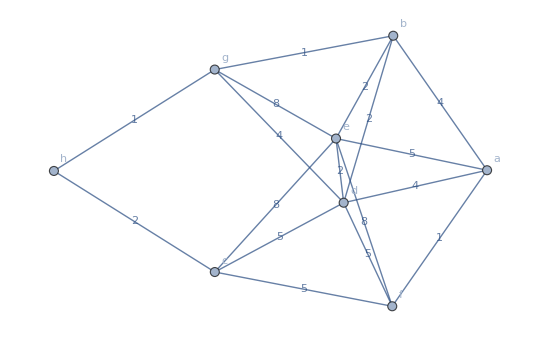

```mathematica
A=({{0, 5, 4, 1, 0, 0, 0, 4}, {5, 0, 2, 8, 0, 8, 8, 2}, {4, 2, 0, 5, 0, 5, 4, 2}, {1, 8, 5, 0, 0, 5, 0, 0}, {0, 0, 0, 0, 0, 2, 1, 0}, {0, 8, 5, 5, 2, 0, 0, 0}, {0, 8, 4, 0, 1, 0, 0, 1}, {4, 2, 2, 0, 0, 0, 1, 0}});
GrafoMP[A,{a,e,d,f,h,c,g,b},mostrarpesos->True]
```

```mathematica
(* Aplicando el algoritmo: *)
```

```mathematica
(* La longitud del camino más corto sería 5 (la marca con la que queda g) *)
```

```mathematica
(*-------------------------------------------------------------------------------*)
```

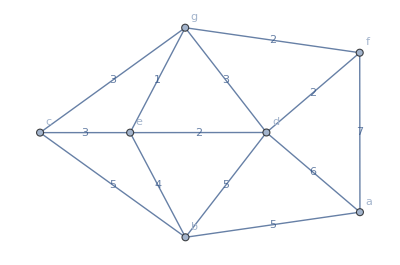

```mathematica
grafo=Grafo[{{a,b},{a,d},{a,f},{b,c},{b,d},{b,e},{c,e},{c,g},{d,e},{d,f},{d,g},{e,g},{f,g}},pesos->{5,6,7,5,5,4,3,3,2,2,3,1,2},mostrarpesos->True]
```

```mathematica
(* Como en la iteracion 4 ocurre un empate entre lo que ya tenia la marca y el resultado de la suma, se tiene que mas bien añadir el nodo en donde ocurrio el empate, en este caso f *)
(* Lo mismo pasa en la iteracion 5, ocurre otro empate, por lo que se agrega el nodo donde ocurrio el empate, o sea e *)
(* Esto lo que significa es que la ruta de longitud mas corta no es unica, en este caso hay tres, una por cada nodo que se empata + la ruta que ya se llevaba *)
```

```mathematica
AlDijkstra[grafo,a,g]
```

La longitud de un camino más corto es: 9

Iteraciones: (a | b | d | f | c | e | g
{0,{}} | {∞,{}} | {∞,{}} | {∞,{}} | {∞,{}} | {∞,{}} | {∞,{}}
{0,{}} | {5,{a}} | {6,{a}} | {7,{a}} | {∞,{}} | {∞,{}} | {∞,{}}
{0,{}} | {5,{a}} | {6,{a}} | {7,{a}} | {10,{b}} | {9,{b}} | {∞,{}}
{0,{}} | {5,{a}} | {6,{a}} | {7,{a}} | {10,{b}} | {8,{d}} | {9,{d}}
{0,{}} | {5,{a}} | {6,{a}} | {7,{a}} | {10,{b}} | {8,{d}} | {9,{d,f}}
{0,{}} | {5,{a}} | {6,{a}} | {7,{a}} | {10,{b}} | {8,{d}} | {9,{d,f,e}}
{0,{}} | {5,{a}} | {6,{a}} | {7,{a}} | {10,{b}} | {8,{d}} | {9,{d,f,e}})

{9.,{{a,d},{d,g}}}

```mathematica
(*-------------------------------------------------------------------------------*)
```

```mathematica
(* Aunque se cambien los pesos por valores negativos, el algoritmo no encuentra siempre correctamente, la longitud del camino mas largo *)
```

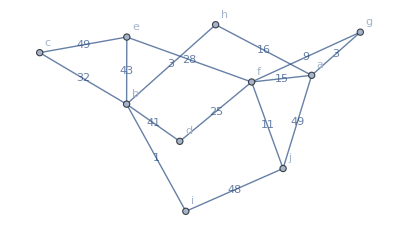

```mathematica
gr1=Grafo[{{a,f},{a,g},{a,h},{a,j},{b,c},{b,d},{b,e},{b,h},{b,i},{c,e},{d,f},{e,f},{f,g},{f,j},{i,j}},pesos->-1{15,3,16,49,32,41,43,3,1,49,25,28,9,11,48},mostrarpesos->True]
```

```mathematica
AlDijkstra[gr1,a,g, all->True]
```

Tabla de pesos del grafo

| a | f | g | h | j | b | c | d | e | i
a | 0 | -15 | -3 | -16 | -49 | 0 | 0 | 0 | 0 | 0
f | -15 | 0 | -9 | 0 | -11 | 0 | 0 | -25 | -28 | 0
g | -3 | -9 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
h | -16 | 0 | 0 | 0 | 0 | -3 | 0 | 0 | 0 | 0
j | -49 | -11 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -48
b | 0 | 0 | 0 | -3 | 0 | 0 | -32 | -41 | -43 | -1
c | 0 | 0 | 0 | 0 | 0 | -32 | 0 | 0 | -49 | 0
d | 0 | -25 | 0 | 0 | 0 | -41 | 0 | 0 | 0 | 0
e | 0 | -28 | 0 | 0 | 0 | -43 | -49 | 0 | 0 | 0
i | 0 | 0 | 0 | 0 | -48 | -1 | 0 | 0 | 0 | 0

Inicialización: {{a,0,{}},{f,∞,{}},{g,∞,{}},{h,∞,{}},{j,∞,{}},{b,∞,{}},{c,∞,{}},{d,∞,{}},{e,∞,{}},{i,∞,{}}}

Se seleccionó el nodo: a

Lista actual de vértices: {f,g,h,j,b,c,d,e,i}

Lista actual de marcas: {{f,-15,{a}},{g,-3,{a}},{h,-16,{a}},{j,-49,{a}},{b,∞,{}},{c,∞,{}},{d,∞,{}},{e,∞,{}},{i,∞,{}}}

Se seleccionó el nodo: j

Lista actual de vértices: {f,g,h,b,c,d,e,i}

Lista actual de marcas: {{f,-60,{j}},{g,-3,{a}},{h,-16,{a}},{b,∞,{}},{c,∞,{}},{d,∞,{}},{e,∞,{}},{i,-97,{j}}}

Se seleccionó el nodo: i

Lista actual de vértices: {f,g,h,b,c,d,e}

Lista actual de marcas: {{f,-60,{j}},{g,-3,{a}},{h,-16,{a}},{b,-98,{i}},{c,∞,{}},{d,∞,{}},{e,∞,{}}}

Se seleccionó el nodo: b

Lista actual de vértices: {f,g,h,c,d,e}

Lista actual de marcas: {{f,-60,{j}},{g,-3,{a}},{h,-101,{b}},{c,-130,{b}},{d,-139,{b}},{e,-141,{b}}}

Se seleccionó el nodo: e

Lista actual de vértices: {f,g,h,c,d}

Lista actual de marcas: {{f,-169,{e}},{g,-3,{a}},{h,-101,{b}},{c,-190,{e}},{d,-139,{b}}}

Se seleccionó el nodo: c

Lista actual de vértices: {f,g,h,d}

Lista actual de marcas: {{f,-169,{e}},{g,-3,{a}},{h,-101,{b}},{d,-139,{b}}}

Se seleccionó el nodo: f

Lista actual de vértices: {g,h,d}

Lista actual de marcas: {{g,-178,{f}},{h,-101,{b}},{d,-194,{f}}}

Se seleccionó el nodo: d

Lista actual de vértices: {g,h}

Lista actual de marcas: {{g,-178,{f}},{h,-101,{b}}}

Se seleccionó el nodo: g

La longitud de un camino más corto es: -178

Lista actual de vértices: {h}

Lista actual de marcas: {{h,-101,{b}}}

Iteraciones: (a | f | g | h | j | b | c | d | e | i
{0,{}} | {∞,{}} | {∞,{}} | {∞,{}} | {∞,{}} | {∞,{}} | {∞,{}} | {∞,{}} | {∞,{}} | {∞,{}}
{0,{}} | {-15,{a}} | {-3,{a}} | {-16,{a}} | {-49,{a}} | {∞,{}} | {∞,{}} | {∞,{}} | {∞,{}} | {∞,{}}
{0,{}} | {-60,{j}} | {-3,{a}} | {-16,{a}} | {-49,{a}} | {∞,{}} | {∞,{}} | {∞,{}} | {∞,{}} | {-97,{j}}
{0,{}} | {-60,{j}} | {-3,{a}} | {-16,{a}} | {-49,{a}} | {-98,{i}} | {∞,{}} | {∞,{}} | {∞,{}} | {-97,{j}}
{0,{}} | {-60,{j}} | {-3,{a}} | {-101,{b}} | {-49,{a}} | {-98,{i}} | {-130,{b}} | {-139,{b}} | {-141,{b}} | {-97,{j}}
{0,{}} | {-169,{e}} | {-3,{a}} | {-101,{b}} | {-49,{a}} | {-98,{i}} | {-190,{e}} | {-139,{b}} | {-141,{b}} | {-97,{j}}
{0,{}} | {-169,{e}} | {-3,{a}} | {-101,{b}} | {-49,{a}} | {-98,{i}} | {-190,{e}} | {-139,{b}} | {-141,{b}} | {-97,{j}}
{0,{}} | {-169,{e}} | {-178,{f}} | {-101,{b}} | {-49,{a}} | {-98,{i}} | {-190,{e}} | {-194,{f}} | {-141,{b}} | {-97,{j}}
{0,{}} | {-169,{e}} | {-178,{f}} | {-101,{b}} | {-49,{a}} | {-98,{i}} | {-190,{e}} | {-194,{f}} | {-141,{b}} | {-97,{j}}
{0,{}} | {-169,{e}} | {-178,{f}} | {-101,{b}} | {-49,{a}} | {-98,{i}} | {-190,{e}} | {-194,{f}} | {-141,{b}} | {-97,{j}})

```mathematica
(* Camino mas largo: g->f->e->b->i->j->a*)
```

```mathematica
AlDijkstraMax[gr1,a,g,all->True]
```

Tabla de pesos del grafo

| a | f | g | h | j | b | c | d | e | i
a | 0 | 15 | 3 | 16 | 49 | 0 | 0 | 0 | 0 | 0
f | 15 | 0 | 9 | 0 | 11 | 0 | 0 | 25 | 28 | 0
g | 3 | 9 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
h | 16 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0
j | 49 | 11 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 48
b | 0 | 0 | 0 | 3 | 0 | 0 | 32 | 41 | 43 | 1
c | 0 | 0 | 0 | 0 | 0 | 32 | 0 | 0 | 49 | 0
d | 0 | 25 | 0 | 0 | 0 | 41 | 0 | 0 | 0 | 0
e | 0 | 28 | 0 | 0 | 0 | 43 | 49 | 0 | 0 | 0
i | 0 | 0 | 0 | 0 | 48 | 1 | 0 | 0 | 0 | 0

Inicialización: {{a,0,{}},{f,-∞,{}},{g,-∞,{}},{h,-∞,{}},{j,-∞,{}},{b,-∞,{}},{c,-∞,{}},{d,-∞,{}},{e,-∞,{}},{i,-∞,{}}}

Se seleccionó el nodo: a

Lista actual de vértices: {f,g,h,j,b,c,d,e,i}

Lista actual de marcas: {{f,15,{a}},{g,3,{a}},{h,16,{a}},{j,49,{a}},{b,-∞,{}},{c,-∞,{}},{d,-∞,{}},{e,-∞,{}},{i,-∞,{}}}

Se seleccionó el nodo: j

Lista actual de vértices: {f,g,h,b,c,d,e,i}

Lista actual de marcas: {{f,60,{j}},{g,3,{a}},{h,16,{a}},{b,-∞,{}},{c,-∞,{}},{d,-∞,{}},{e,-∞,{}},{i,97,{j}}}

Se seleccionó el nodo: i

Lista actual de vértices: {f,g,h,b,c,d,e}

Lista actual de marcas: {{f,60,{j}},{g,3,{a}},{h,16,{a}},{b,98,{i}},{c,-∞,{}},{d,-∞,{}},{e,-∞,{}}}

Se seleccionó el nodo: b

Lista actual de vértices: {f,g,h,c,d,e}

Lista actual de marcas: {{f,60,{j}},{g,3,{a}},{h,101,{b}},{c,130,{b}},{d,139,{b}},{e,141,{b}}}

Se seleccionó el nodo: e

Lista actual de vértices: {f,g,h,c,d}

Lista actual de marcas: {{f,169,{e}},{g,3,{a}},{h,101,{b}},{c,190,{e}},{d,139,{b}}}

Se seleccionó el nodo: c

Lista actual de vértices: {f,g,h,d}

Lista actual de marcas: {{f,169,{e}},{g,3,{a}},{h,101,{b}},{d,139,{b}}}

Se seleccionó el nodo: f

Lista actual de vértices: {g,h,d}

Lista actual de marcas: {{g,178,{f}},{h,101,{b}},{d,194,{f}}}

Se seleccionó el nodo: d

Lista actual de vértices: {g,h}

Lista actual de marcas: {{g,178,{f}},{h,101,{b}}}

Se seleccionó el nodo: g

La longitud de un camino más largo es: 178

Lista actual de vértices: {h}

Lista actual de marcas: {{h,101,{b}}}

Iteraciones: (a | f | g | h | j | b | c | d | e | i
{0,{}} | {-∞,{}} | {-∞,{}} | {-∞,{}} | {-∞,{}} | {-∞,{}} | {-∞,{}} | {-∞,{}} | {-∞,{}} | {-∞,{}}
{0,{}} | {15,{a}} | {3,{a}} | {16,{a}} | {49,{a}} | {-∞,{}} | {-∞,{}} | {-∞,{}} | {-∞,{}} | {-∞,{}}
{0,{}} | {60,{j}} | {3,{a}} | {16,{a}} | {49,{a}} | {-∞,{}} | {-∞,{}} | {-∞,{}} | {-∞,{}} | {97,{j}}
{0,{}} | {60,{j}} | {3,{a}} | {16,{a}} | {49,{a}} | {98,{i}} | {-∞,{}} | {-∞,{}} | {-∞,{}} | {97,{j}}
{0,{}} | {60,{j}} | {3,{a}} | {101,{b}} | {49,{a}} | {98,{i}} | {130,{b}} | {139,{b}} | {141,{b}} | {97,{j}}
{0,{}} | {169,{e}} | {3,{a}} | {101,{b}} | {49,{a}} | {98,{i}} | {190,{e}} | {139,{b}} | {141,{b}} | {97,{j}}
{0,{}} | {169,{e}} | {3,{a}} | {101,{b}} | {49,{a}} | {98,{i}} | {190,{e}} | {139,{b}} | {141,{b}} | {97,{j}}
{0,{}} | {169,{e}} | {178,{f}} | {101,{b}} | {49,{a}} | {98,{i}} | {190,{e}} | {194,{f}} | {141,{b}} | {97,{j}}
{0,{}} | {169,{e}} | {178,{f}} | {101,{b}} | {49,{a}} | {98,{i}} | {190,{e}} | {194,{f}} | {141,{b}} | {97,{j}}
{0,{}} | {169,{e}} | {178,{f}} | {101,{b}} | {49,{a}} | {98,{i}} | {190,{e}} | {194,{f}} | {141,{b}} | {97,{j}})